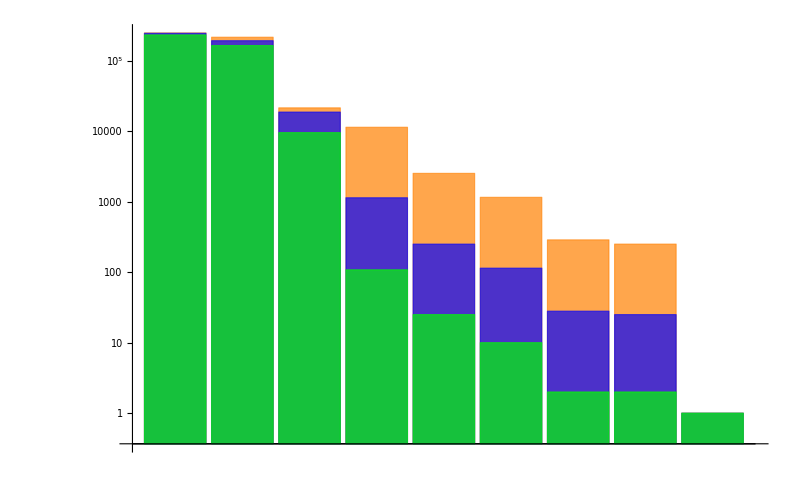

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[BarChart,BaseStyle->{FontSize->20}];
data1 = Import[y<>"/averageResults/dataUniversity-0.01-turtles.csv"];
data2 = Import[y<>"/averageResults/dataUniversity-0.001-turtles.csv"];
data3 = Import[y<>"/averageResults/dataUniversity-1.0E-4-turtles.csv"];
Fdata1 = Flatten[data1];
Fdata2 = Flatten[data2];
Fdata3 = Flatten[data3];

plot=Legended[Show[{{BarChart[{Fdata1},ImageSize->800,  ChartStyle->{Directive[Orange,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log", ChartLabels->{"MP1", "MP2","CP1", "MP3","MP4", "CP2","CP3", "CP4",}], BarChart[{Fdata2},ImageSize->800, ChartStyle->{Directive[Blue,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"], BarChart[{Fdata3},ImageSize->800, ChartStyle->{Directive[Green,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"]}}, Frame->{{True, None},{True, None}}, FrameLabel->{"Universidades","Publicaciones"}], Placed[SwatchLegend[{Directive[Orange,Opacity[.5]],Directive[Blue,Opacity[.5]],Directive[Green,Opacity[.5]]},{Style["I1",17],Style["I2",17],Style["I3",17]},LegendMargins->{{35,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.7,0.7},{0,0}}]];
Export["DistribucionProductividadUniversidades.png",plot];

Show[BarChart[{Fdata1},ImageSize->800,  ChartStyle->{Directive[Orange,Opacity[.7]]}, ScalingFunctions->"Log"],BarChart[{Fdata2},ImageSize->800, ChartStyle->{Directive[Blue,Opacity[.7]]}, Axes->{False, False}, ScalingFunctions->"Log"],BarChart[{Fdata3},ImageSize->800, ChartStyle->{Directive[Green,Opacity[.7]]}, Axes->{False, False}, ScalingFunctions->"Log"],FrameLabel->{{"Publicaciones"},{"Numero de Universidades"}}]
```

```mathematica
]
```